```mathematica
SI Appendix for Indirect reciprocity with Bayesian reasoning
B. Morsky, J. Plotkin, E. Akçay
```

```mathematica
SetDirectory["/Users/brycemorsky/Desktop/New projects/Indirect reciprocity/figures"];
```

## Scoring

```mathematica
Clear["Global`*"]
pix=r*(x+Qcg*z)-1;
piy=r*(x+Qdg*z);
piz=r*(x+(g*Qcg+(1-g)*Qdg)*z)-g;
pibar=x*pix+(1-x-z)*piy+z*piz;
FullSimplify[(pix-pibar)*x]
FullSimplify[(piy-pibar)*y]
FullSimplify[(piz-pibar)*z]
```

-x (-1+x+g z) (-1+(Qcg-Qdg) r z)

-y (x+g z) (-1+(Qcg-Qdg) r z)

-(x+g (-1+z)) z (-1+(Qcg-Qdg) r z)

```mathematica
Clear["Global`*"]
Pc=ϵ*g/(ϵ*g+e*(1-g));
Pd=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Qc=ϵ*Pc+(1-ϵ)*Pd;
Qd=(1-e)*Pd+e*Pc;
(* gz=g with no bias *)
FullSimplify[Qc*g+Qd*(1-g)]
```

g

### Theorem A.1.1

```mathematica
(* Equilibrium g of the reputation system in the interior of the simplex *)
{fx,fy,fz}={Qc-gx,Qd-gy,Qc*g+Qd*(1-g)-gz};
FullSimplify[g-x*Qc-y*Qd-(1-x-y)*(g*Qc+(1-g)*Qd)]
Solve[g==x*Qc+y*Qd+(1-x-y)*(Qc*g+Qd*(1-g)),g]
(* Eigenvalues of the Jacobian for equilibrium g=0 in the interior of the simplex *)
FullSimplify[Eigenvalues[D[{fx,fy,fz}/.{g->gx*x+gy*y+gz*(1-x-y)},{{gx,gy,gz}}]/.{gx->0,gy->0,gz->0}]]
(* Eigenvalues of the Jacobian for equilibrium g=1 in the interior of the simplex *)
FullSimplify[Eigenvalues[D[{fx,fy,fz}/.{g->gx*x+gy*y+gz*(1-x-y)},{{gx,gy,gz}}]/.{gx->1,gy->1,gz->1}]]
(* Equilibria gx, gy, and gz, and eigenvalues of the Jacobian for equilibrium g=x/x+y in the interior of the simplex *)
gxeq=FullSimplify[Qc/.{g->x/(x+y)}]
gyeq=FullSimplify[Qd/.{g->x/(x+y)}]
gzeq=FullSimplify[Qc*g+Qd*(1-g)/.{g->x/(x+y)}]
FullSimplify[Eigenvalues[D[{fx,fy,fz}/.{g->gx*x+gy*y+gz*(1-x-y)},{{gx,gy,gz}}]/.{gx->gxeq,gy->gyeq,gz->gzeq}]]
(* Show dz/dt = 0 *)
pix=r*(x+Qcg*z)-1;
piy=r*(x+Qdg*z);
piz=r*(x+(g*Qcg+(1-g)*Qdg)*z)-g;
pibar=x*pix+(1-x-z)*piy+z*piz;
FullSimplify[(piz-pibar)*z]
(* Equilibrium g of the reputation system on the AllC-Disc boundary *)
FullSimplify[g-x*Qc-(1-x)*(g*Qc+(1-g)*Qd)]
Solve[g==x*Qc+(1-x)*(Qc*g+Qd*(1-g)),g]
(* Eigenvalues of the Jacobian for equilibrium g=0 on the AllC-Disc boundary *)
FullSimplify[Eigenvalues[D[{fx,fz}/.{g->gx*x+gz*(1-x)},{{gx,gz}}]/.{gx->0,gz->0}]]
(* Equilibrium g of the reputation system on the AllD-Disc boundary *)
FullSimplify[g-y*Qd-(1-y)*(g*Qc+(1-g)*Qd)]
Solve[g==y*Qd+(1-y)*(Qc*g+Qd*(1-g)),g]
(* Eigenvalues of the Jacobian for equilibrium g=1 on the AllD-Disc boundary *)
FullSimplify[Eigenvalues[D[{fy,fz}/.{g->gy*y+gz*(1-y)},{{gy,gz}}]/.{gy->1,gz->1}]]
```

((-1+g) g ((-1+g) x+g y) (e-ϵ)^2)/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

{{g→0},{g→1},{g→x/(x+y)}}

{-1,-1,-(x (e-ϵ)^2)/((-1+e) e)}

{-(y (e-ϵ)^2)/((-1+ϵ) ϵ),-1,-1}

(x (e y (-1+2 ϵ)+ϵ (x (-1+ϵ)-y ϵ)))/(((-1+e) y+x (-1+ϵ)) (e y+x ϵ))

(x ((-1+e) e y+x (-1+ϵ) ϵ))/(((-1+e) y+x (-1+ϵ)) (e y+x ϵ))

x/(x+y)

{(x y (x+y) (e-ϵ)^2)/(((-1+e) y+x (-1+ϵ)) (e y+x ϵ)),-1,-1}

-(x+g (-1+z)) z (-1+(Qcg-Qdg) r z)

((-1+g)^2 g x (e-ϵ)^2)/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

{{g→0},{g→1},{g→1}}

{-1,-(x (e-ϵ)^2)/((-1+e) e)}

((-1+g) g^2 y (e-ϵ)^2)/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

{{g→0},{g→0},{g→1}}

{-(y (e-ϵ)^2)/((-1+ϵ) ϵ),-1}

### Theorem A.1.2

```mathematica
(* Simplify r*z*(Qc-Qd)-1 at g=x/(1-z)*)
sol=FullSimplify[r*z*(Qc-Qd)-1/.{g->x/(1-z)}]
(* Collect coefficients for numerator of r*z*(Qc-Qd)-1, note we take the negative of sol, since the denominator is negative *)
FullSimplify[CoefficientList[Numerator[-sol],x]]
(* r*z*(Qc-Qd)-1 = -1 when x=0 or 1 *)
FullSimplify[r*z*(Qc-Qd)-1//.{g->0,x->0}]
FullSimplify[r*z*(Qc-Qd)-1//.{g->1,x->1}]
```

(e (-1+x+z) (-1+e+z-e z+e x (-1+r z))-x (-1+z+2 e (-1+x+z) (-1+r z)) ϵ+x (r (-1+z) z+x (-1+r z)) ϵ^2)/((e (-1+x+z)-x ϵ) (1-z+e (-1+x+z)-x ϵ))

{(-1+e) e (-1+z)^2,-(-1+z) (e-ϵ) (1+e (-2+r z)-r z ϵ),-(-1+r z) (e-ϵ)^2}

-1

-1

```mathematica
(* d(Qcg-Qdg)/de1 < 0 and d(Qcg-Qdg)/de2 < 0 *)
FullSimplify[D[Evaluate[Qc-Qd/.{ϵ->(1-e1)*(1-e2)+e1*e2,e->e2}],e1]]
FullSimplify[D[Evaluate[Qc-Qd/.{ϵ->(1-e1)*(1-e2)+e1*e2,e->e2}],e2]]
```

((-1+e1) (1-2 e2)^2 (-1+g) g (2 (-1+e2) e2+(-1+e1) (1-2 e2)^2 g))/((-1+e2+(-1+e1) (-1+2 e2) g)^2 (e2+(-1+e1) (-1+2 e2) g)^2)

-((-1+e1)^2 (-1+2 e2) (-1+g) g)/((-1+e2+(-1+e1) (-1+2 e2) g)^2 (e2+(-1+e1) (-1+2 e2) g)^2)

## Simple Standing

```mathematica
Clear["Global`*"]
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=1;
Qdb=1;
(* gz=g with no bias *)
(*{fy,fz}={Qdg*g+1-g-gy,Qcg*g+1-g-gz//.{g->(1-z)*gy+z*gz}};
{geq1,geq2,geq3}=Solve[g==(Qcg*g+1-g)*z+(Qdg*g+1-g)*(1-z),g];
{gyeq1,gzeq1}={Qdg*g+1-g,Qcg*g+1-g}/.geq1;
{gyeq2,gzeq2}={Qdg*g+1-g,Qcg*g+1-g}/.geq2;
{gyeq3,gzeq3}={Qdg*g+1-g,Qcg*g+1-g}/.geq3;
Solve[g==(1-z)*(Qdg*g+1-g)+z*(Qcg*g+1-g),g];
Eigenvalues[D[{fy,fz},{{gy,gz}}]/.{g->1,gy->1,gz->1}];
FullSimplify[{c0,c1,c2}=CoefficientList[CharacteristicPolynomial[D[{fy,fz},{{gy,gz}}],λ],λ]];*)
```

```mathematica
FullSimplify[c0//.{gy->gyeq2,gz->gzeq2,ϵ->0.9802,e->0.01,z->0.6}]
```

1.0034

```mathematica
Clear["Global`*"]
{fy,fz}={Qdg[g[gx,gy]]*g[gx,gy]+1-g[gx,gy]-gy,Qcg[g[gx,gy]]*g[gx,gy]+1-g[gx,gy]-gz};
CoefficientList[CharacteristicPolynomial[D[{fy,fz},{{gy,gz}}],λ],λ]
```

{1+g^(0,1)[gx,gy]-Qdg[g[gx,gy]] g^(0,1)[gx,gy]-g[gx,gy] Qdg'[g[gx,gy]] g^(0,1)[gx,gy],2+g^(0,1)[gx,gy]-Qdg[g[gx,gy]] g^(0,1)[gx,gy]-g[gx,gy] Qdg'[g[gx,gy]] g^(0,1)[gx,gy],1}

```mathematica
FullSimplify[(1-z)*(Qdg*g+1-g)+z*(Qcg*g+1-g)-g]
```

(-1+e)^2 (-1+4 e)

```mathematica
FullSimplify[(1-z)*(Qdg*g+1-g)+z*Qcg*g+1-g]
```

e (-3+e (5-2 z)+z)+(-1+2 e) (-2+z) ϵ

```mathematica
Clear["Global`*"]
{fy,fz}={Qdg[g]*g+1-g-gy,Qcg[g]*g+1-g-gz}//.{g->(1-z)*gy+z*gz};
MatrixForm[D[{fy,fz},{{gy,gz}}]]
```

(-2+z+(1-z) Qdg[gy (1-z)+gz z]+(1-z) (gy (1-z)+gz z) Qdg'[gy (1-z)+gz z] | -z+z Qdg[gy (1-z)+gz z]+z (gy (1-z)+gz z) Qdg'[gy (1-z)+gz z]
-1+z+(1-z) Qcg[gy (1-z)+gz z]+(1-z) (gy (1-z)+gz z) Qcg'[gy (1-z)+gz z] | -1-z+z Qcg[gy (1-z)+gz z]+z (gy (1-z)+gz z) Qcg'[gy (1-z)+gz z])

```mathematica
Clear["Global`*"]
J={{a*g+(Qd-1)*(1-z)-1,b*g+z*(Qd-1)},{c*g+(Qc-1)*(1-z),d*g+z*(Qc-1)-1}}
Collect[CharacteristicPolynomial[J,λ],λ]
```

{{-1+a g+(-1+Qd) (1-z),b g+(-1+Qd) z},{c g+(-1+Qc) (1-z),-1+d g+(-1+Qc) z}}

2-a g+b g-2 d g-b c g^2+a d g^2-b g Qc-Qd+d g Qd-a g z-b g z+c g z+d g z-Qc z+a g Qc z+b g Qc z+Qd z-c g Qd z-d g Qd z+(3-a g-d g-Qd-Qc z+Qd z) λ+λ^2

### Theorem A.3.2

```mathematica
(* The numerator of Qcg*g + 1-2*g *)
num=FullSimplify[(ϵ^2*hatg*((1-ϵ)*hatg+(1-e)*(1-hatg)) + (1-ϵ)^2*hatg*(ϵ*hatg+e*(1-hatg)))*g +(1-2*g)*((1-ϵ)*hatg+(1-e)*(1-hatg))*(ϵ*hatg+e*(1-hatg))/.ghat->(1-λ)*g+λ/.{hatg->(1-λ)*g+λ}]
(* Coefficients for polynomial *)
{c0,c1,c2}=FullSimplify[CoefficientList[FullSimplify[num/(1-g)],g]]
(* Polynomial at g=1 *)
FullSimplify[c2+c1+c0]
```

(-1+g) (e^2 (-1+g) (-1+2 g) (-1+λ)^2-e (-1+g) (-1+λ) (1+g (1+2 ϵ) (-1+λ)-2 ϵ λ)+ϵ (g (-1+λ)-λ) (1+g (-1+λ)-ϵ λ))

{-(e (-1+λ)-ϵ λ) (1+e (-1+λ)-ϵ λ),(-1+λ) (2 e-3 e^2-ϵ+2 e ϵ+(1-3 e+ϵ) (-e+ϵ) λ),-(-1+2 e) (e-ϵ) (-1+λ)^2}

-(-1+ϵ) ϵ λ

### Theorem A.3.3

```mathematica
(* Calculate (dQcg/dg)*g*z + (dQdg/dg)*g*(1-z) - 1 *)
FullSimplify[D[Qdg,g]*g*(1-z)+D[Qcg,g]*g*z-1/.{z->(2-1/g-Qdg)/(Qcg-Qdg)}]
```

-((-1+g) (e^2 (-1+g+g^2)+g^2 ϵ^2-e (-1+g+2 g^2 ϵ)))/(g (e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

### Convergence

```mathematica
M=Array[m,{24*2,2}];
e1=0.01;
e=0.01;
ϵ=(1-e1)*(1-e)+e1*e;
Do[
z=0.01*i;
{fy,fz}={Qdg*g+1-g-gy,Qcg*g+1-g-gz//.{g->(1-z)*gy+z*gz}};
geq=Select[g/.Solve[g==(Qcg*g+1-g)*z+(Qdg*g+1-g)*(1-z),g],0<#<1&][[1]];
{gyeq,gzeq}={Qdg*g+1-g,Qcg*g+1-g}/.{g->geq};
eigs=Eigenvalues[D[{fy,fz},{{gy,gz}}]//.{g->geq,gy->gyeq,gz->gzeq}];M[[i/4]]={z,eigs[[1]]};
M[[i/4+24]]={z,eigs[[2]]};
,{i,4,96,4}]
eigenImage=ListPlot[M,LabelStyle->"20",ImageSize->Large,PlotStyle->{Directive[Blue,PointSize[Large]]},PlotMarkers->Automatic,BaseStyle->{FontSize->28},PlotRange->{{0,1},{-1.005,-0.96}},Frame->{{True,True},{True,True}},FrameStyle->{{Black,Black},{Black,Black}},AspectRatio->1,FrameLabel->{Framed[Style["Discriminators, z"],FrameStyle->None],"Eigenvalues"}];
Export["eigen_SS_public.pdf",eigenImage];
```

## Staying

```mathematica
Clear["Global`*"]
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
```

### Theorem A.4.2

### Theorem A.4.3

```mathematica
(* Calculate (dQcg/dg)*z + (dQdg/dg)*(1-z) - 1 *)
FullSimplify[D[Qdg,g]*(1-z)+D[Qcg,g]*z-1/.{z->(g-Qdg)/(Qcg-Qdg)}]
```

-((-1+g) g (e-ϵ)^2)/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

### Convergence

```mathematica
M=Array[m,{24*2,2}];
e1=0.01;
e=0.01;
ϵ=(1-e1)*(1-e)+e1*e;
Do[
z=0.01*i;
{fy,fz}={Qdg-gy,Qcg-gz//.{g->(1-z)*gy+z*gz}};
geq=Select[g/.Solve[g==Qcg*z+Qdg*(1-z),g],0<#<1&][[1]];
{gyeq,gzeq}={Qdg,Qcg}/.{g->geq};
eigs=Eigenvalues[D[{fy,fz},{{gy,gz}}]//.{g->geq,gy->gyeq,gz->gzeq}];M[[i/4]]={z,eigs[[1]]};
M[[i/4+24]]={z,eigs[[2]]};
,{i,4,96,4}]
eigenImage=ListPlot[M,LabelStyle->"20",ImageSize->Large,PlotStyle->{Directive[Blue,PointSize[Large]]},PlotMarkers->Automatic,BaseStyle->{FontSize->28},PlotRange->{{0,1},{-1.005,-0.8}},Frame->{{True,True},{True,True}},FrameStyle->{{Black,Black},{Black,Black}},AspectRatio->1,FrameLabel->{Framed[Style["Discriminators, z"],FrameStyle->None],"Eigenvalues"}];
Export["eigen_St_public.pdf",eigenImage];
```

## Stern Judging

```mathematica
Clear["Global`*"]
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Pcb=e*g/(e*g+ϵ*(1-g));
Pdb=(1-e)*g/((1-e)*g+(1-ϵ)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
```

### Theorem A.5.1

```mathematica
(* Calculate Qdb - Qcg > 0 for g > 1/2 *)
FullSimplify[Qdb-Qcg]
```

((-1+g)^2 g (-1+2 g) (e-ϵ)^3 (-1+e+ϵ))/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ) (-1+e g+ϵ-g ϵ) (e g+ϵ-g ϵ))

```mathematica
FullSimplify[-1+e+ϵ/.{ϵ->(1-e)(1-e1)+e1*e}]
```

(-1+2 e) e1

### Theorem A.5.3

```mathematica
(* Calculate Qcg - Qdb *)
FullSimplify[Qcg - Qdb]
```

-((-1+g)^2 g (-1+2 g) (e-ϵ)^3 (-1+e+ϵ))/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ) (-1+e g+ϵ-g ϵ) (e g+ϵ-g ϵ))

```mathematica
(* Calculate (dQcg/dg)*z + (dQdg/dg)*(1-z) - 1 *)
FullSimplify[Qdg*(1-z)+Qcg*z-1/.{z->(g-Qdg*g-Qdb*(1-g))/(g*Qcg-g*Qdg)}]
```

((-1+g) (e^2 (-1+2 g)+(-1+g) ϵ-e (g+2 (-1+g) ϵ)))/((-1+e g+ϵ-g ϵ) (e g+ϵ-g ϵ))

```mathematica
(* Calculate dQdb/dg - 1 *)
FullSimplify[D[Qdb,g] - 1]
```

-((-1+g) (e-ϵ)^2 (e g^2 (-2+e+e g)+ϵ+g (-3+2 g (1+e-e g)) ϵ+(-1+g)^3 ϵ^2))/((-1+e g+ϵ-g ϵ)^2 (e g+ϵ-g ϵ)^2)

### Convergence

```mathematica
M=Array[m,{24*2,2}];
e1=0.01;
e=0.01;
ϵ=(1-e1)*(1-e)+e1*e;
Do[
z=0.01*i;
{fy,fz}={Qdg*g+Qdb*(1-g)-gy,Qcg*g+Qdb*(1-g)-gz//.{g->(1-z)*gy+z*gz}};
geq=Select[g/.Solve[g==Qcg*z+Qdg*(1-z),g],0<#<1&][[1]];
{gyeq,gzeq}={Qdg,Qcg}/.{g->geq};
eigs=Eigenvalues[D[{fy,fz},{{gy,gz}}]//.{g->geq,gy->gyeq,gz->gzeq}];M[[i/4]]={z,eigs[[1]]};
M[[i/4+24]]={z,eigs[[2]]};
,{i,4,96,4}]
eigenImage=ListPlot[M,LabelStyle->"20",ImageSize->Large,PlotStyle->{Directive[Blue,PointSize[Large]]},PlotMarkers->Automatic,BaseStyle->{FontSize->28},PlotRange->{{0,1},{-1.005,-0.8}},Frame->{{True,True},{True,True}},FrameStyle->{{Black,Black},{Black,Black}},AspectRatio->1,FrameLabel->{Framed[Style["Discriminators, z"],FrameStyle->None],"Eigenvalues"}];
Export["eigen_SJ_public.pdf",eigenImage];
```

## Public assessment: Theorem A.3.2

```mathematica
Clear["Global`*"]
```

```mathematica
eq=FullSimplify[Solve[g*Qdg*(1-z)+z*g*Qcg+1-g==g,g]][[2]]
```

{g→-(3 e^2+ϵ-2 e (1+ϵ)+√(e^3 (4-3 e+4 (-1+e) z)+2 e^2 (-3+2 e+4 z-4 e z) ϵ+(1+4 (-1+e) e z) ϵ^2))/(2 (e-ϵ) (1+e (-3+z)+ϵ-z ϵ))}

```mathematica
(Q\cg-Q\dg)(g-g_2)z=g(Q\cg-2)+1
```

```mathematica
FullSimplify[g*Qdg*(1-z)+z*g*Qcg+1-2*g]
```

((-1+g) (e^2 (-1+g (3+g (-3+z)))+e ((-1+g)^2-2 g (1+g (-2+z)) ϵ)+g ϵ (1+g (-1+(-1+z) ϵ))))/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

```mathematica
Collect[(e^2 (-1+g (3+g (-3+z)))+e ((-1+g)^2-2 g (1+g (-2+z)) ϵ)+g ϵ (1+g (-1+(-1+z) ϵ))),g]
```

e-e^2+g (-2 e+3 e^2+ϵ-2 e ϵ)+g^2 (e+e^2 (-3+z)-2 e (-2+z) ϵ+ϵ (-1+(-1+z) ϵ))

```mathematica
condition=FullSimplify[D[Qdg,g]*(1-z)-g/.{g->1}]
```

(e^2 (-1+z)-2 e (-1+z) ϵ+(z-ϵ) ϵ)/((-1+ϵ) ϵ)

```mathematica
FullSimplify[D[Qdg,g]*(1-z)+D[Qcg,g]*z-1/.{g->1}]
```

```mathematica
TeXForm[((-1+z) (e-ϵ)^2)/((-1+ϵ) ϵ)]
```

\frac{(z-1) (e-\epsilon )^2}{(\epsilon -1) \epsilon }

```mathematica
Collect[e^2 (1+g (-4-3 (-2+g) g))+g (-1+g (2+g (-2+ϵ))) ϵ+e (-1+g) (1+2 (-1+g) g (1+ϵ)),g]
```

```mathematica
Collect[e^2 (1+g (-4-3 (-2+g) g))+g (-1+g (2+g (-2+ϵ))) ϵ+e (-1+g) (1+2 (-1+g) g (1+ϵ))/.{g->g+δ},g]
```

```mathematica
FullSimplify[-e+e^2+e δ-4 e^2 δ+6 e^2 δ^2-3 e^2 δ^3-δ ϵ+2 δ^2 ϵ+δ^3 (-2+ϵ) ϵ+2 e δ (1+ϵ)-4 e δ^2 (1+ϵ)+2 e δ^3 (1+ϵ)+g^3 (-3 e^2+(-2+ϵ) ϵ+2 e (1+ϵ))+g^2 (6 e^2-9 e^2 δ+2 ϵ+3 δ (-2+ϵ) ϵ-4 e (1+ϵ)+6 e δ (1+ϵ))+g (e-4 e^2+12 e^2 δ-9 e^2 δ^2-ϵ+4 δ ϵ+3 δ^2 (-2+ϵ) ϵ+2 e (1+ϵ)-8 e δ (1+ϵ)+6 e δ^2 (1+ϵ))-(e^2 (1+g (-4-3 (-2+g) g))+g (-1+g (2+g (-2+ϵ))) ϵ+e (-1+g) (1+2 (-1+g) g (1+ϵ)))]
```

```mathematica
Collect[δ (-e^2 (4+9 g^2+3 (-2+δ) δ+3 g (-4+3 δ))+(-1+δ (2+δ (-2+ϵ))+g (4+3 δ (-2+ϵ))+3 g^2 (-2+ϵ)) ϵ+e (3+2 ϵ+6 g^2 (1+ϵ)+2 (-2+δ) δ (1+ϵ)+2 g (-4+3 δ) (1+ϵ))),δ]
```

δ^3 (-3 e^2+(-2+ϵ) ϵ+2 e (1+ϵ))+δ^2 (6 e^2-9 e^2 g+2 ϵ+3 g (-2+ϵ) ϵ-4 e (1+ϵ)+6 e g (1+ϵ))+δ (3 e-4 e^2+12 e^2 g-9 e^2 g^2-ϵ+2 e ϵ+4 g ϵ+3 g^2 (-2+ϵ) ϵ-8 e g (1+ϵ)+6 e g^2 (1+ϵ))

```mathematica
FullSimplify[3 e-4 e^2+12 e^2 g-9 e^2 g^2-ϵ+2 e ϵ+4 g ϵ+3 g^2 (-2+ϵ) ϵ-8 e g (1+ϵ)+6 e g^2 (1+ϵ)]
```

```mathematica
Assuming[1>g>0&&1>ϵ>0.5>e>0&&1>e1>0&&ϵ==(1-e)*(1-e1)+e*e1&&1>z>0,FullSimplify@Reduce[e^2 (-1+z)-2 e (-1+z) ϵ+(z-ϵ) ϵ< 0]]
```

z<(e-ϵ)^2/(e^2+ϵ-2 e ϵ)

```mathematica
Assuming[1>g>0&&1>ϵ>0.5>e>0&&1>e1>0&&ϵ==(1-e)*(1-e1)+e*e1&&1>z>0,FullSimplify@Reduce[(12 e^2+4 ϵ-8 e (1+ϵ))≤0]]
```

3 e^2+ϵ≤2 e (1+ϵ)

```mathematica
eq5=FullSimplify[D[Qdg,g]*(1-z)+D[Qcg,g]*z-1]
```

-((e-ϵ)^2 (e^2 (-1+g)^2 ((-2+g) g+z)+g^2 ϵ (1-2 g+z+g^2 ϵ-z ϵ)-e (-1+g)^2 (z+2 g (-1+g ϵ))))/((-1+e-e g+g ϵ)^2 (e-e g+g ϵ)^2)

```mathematica
FullSimplify[D[Qdg,g]*(1-z)+D[Qcg,g]*z-g/.{g->1}]
```

((-1+z) (e-ϵ)^2)/((-1+ϵ) ϵ)

```mathematica
Assuming[1>ϵ>0.5>e>0&&1>e1>0&&ϵ==(1-e)*(1-e1)+e*e1&&1>z>0,FullSimplify@Reduce[(-e^2 (1+z)+2 e (1+z) ϵ+ϵ (z-ϵ-2 z ϵ))/((-1+ϵ) ϵ)>0]]
```

1+2 e+√(1-4 (-1+e) e)==4 ϵ||(z>-(e-ϵ)^2/(e^2-2 e ϵ+ϵ (-1+2 ϵ))&&1+2 e+√(1-4 (-1+e) e)<4 ϵ)||(z<-(e-ϵ)^2/(e^2-2 e ϵ+ϵ (-1+2 ϵ))&&1+2 e+√(1-4 (-1+e) e)>4 ϵ)

```mathematica
FullSimplify[g*Qdg*(1-z)+z*g*Qcg+1-2*g]
```

((-1+g) (e^2 (-1+g (3+g (-3+z)))+e ((-1+g)^2-2 g (1+g (-2+z)) ϵ)+g ϵ (1+g (-1+(-1+z) ϵ))))/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

```mathematica
Assuming[1>g>0&&1>ϵ>0.5>e>0&&1>e1>0&&ϵ==(1-e)*(1-e1)+e*e1&&1>z>0,FullSimplify@Reduce[(-4 e+6 e^2+2 ϵ-4 e ϵ+√(-2 e^2+3 e^3+8 e ϵ-7 e^2 ϵ-6 e^3 ϵ-2 ϵ^2-7 e ϵ^2+16 e^2 ϵ^2+3 ϵ^3-6 e ϵ^3))/(3 (-2 e+3 e^2+2 ϵ-2 e ϵ-ϵ^2))≤0]]
```

ϵ≥Root[2 e^2-3 e^3+(-8 e+7 e^2+6 e^3) #1+(2+7 e-16 e^2) #1^2+(-3+6 e) #1^3&,3]&&√(21 (-11+8 √2))+14 e>7

```mathematica
Solve[3 e-4 e^2+12 e^2 g-9 e^2 g^2-ϵ+2 e ϵ+4 g ϵ+3 g^2 (-2+ϵ) ϵ-8 e g (1+ϵ)+6 e g^2 (1+ϵ)==0,g]
```

{{g→(-4 e+6 e^2+2 ϵ-4 e ϵ-√(-2 e^2+3 e^3+8 e ϵ-7 e^2 ϵ-6 e^3 ϵ-2 ϵ^2-7 e ϵ^2+16 e^2 ϵ^2+3 ϵ^3-6 e ϵ^3))/(3 (-2 e+3 e^2+2 ϵ-2 e ϵ-ϵ^2))},{g→(-4 e+6 e^2+2 ϵ-4 e ϵ+√(-2 e^2+3 e^3+8 e ϵ-7 e^2 ϵ-6 e^3 ϵ-2 ϵ^2-7 e ϵ^2+16 e^2 ϵ^2+3 ϵ^3-6 e ϵ^3))/(3 (-2 e+3 e^2+2 ϵ-2 e ϵ-ϵ^2))}}

```mathematica
Collect[-e^2 (2-3 g)^2+(-1+g (4+3 g (-2+ϵ))) ϵ+e (3+2 ϵ+2 g (-4+3 g) (1+ϵ)),g]
```

3 e-4 e^2-ϵ+2 e ϵ+g (12 e^2+4 ϵ-8 e (1+ϵ))+g^2 (-9 e^2+3 (-2+ϵ) ϵ+6 e (1+ϵ))

```mathematica
FullSimplify[Together[3 e-4 e^2-ϵ+2 e ϵ]]
```

(e^2 (1+g (-4-3 (-2+g) g))+g (-1+g (2+g (-2+ϵ))) ϵ+e (-1+g) (1+2 (-1+g) g (1+ϵ)))/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

```mathematica
Solve[Qdg*g+1-2*g==0,g]
```

{{g→1},{g→(-2 e+3 e^2+ϵ-2 e ϵ-√(4 e^3-3 e^4-6 e^2 ϵ+4 e^3 ϵ+ϵ^2))/(2 (-e+3 e^2+ϵ-4 e ϵ+ϵ^2))},{g→(-2 e+3 e^2+ϵ-2 e ϵ+√(4 e^3-3 e^4-6 e^2 ϵ+4 e^3 ϵ+ϵ^2))/(2 (-e+3 e^2+ϵ-4 e ϵ+ϵ^2))}}

```mathematica
FullSimplify[D[Qdg,g]*(1-z)-g/.{g->1}]
```

(e^2 (-1+z)-2 e (-1+z) ϵ+(z-ϵ) ϵ)/((-1+ϵ) ϵ)

```mathematica
Assuming[1>ϵ>0.5>e>0&&1>e1>0&&ϵ==(1-e)*(1-e1)+e*e1&&1>z>0,FullSimplify@Reduce[condition≤0]]
```

$Aborted

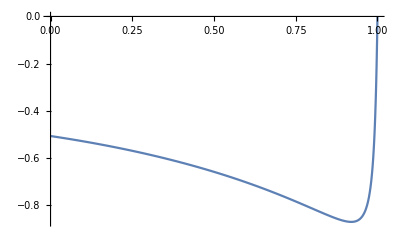

```mathematica
Plot[Evaluate[D[Qcg,g]*(z)-g/.eq/.{e->0.01,ϵ->0.98}],{z,0,1}]
```

```mathematica
Solve[1-p-θ*(1-2*p)^2==p+1/(2*θ)-θ*(p+1/(2*θ)-p)^2,p]
```

{{p→(-1+2 θ)/(4 θ)},{p→(-1+2 θ)/(4 θ)}}

```mathematica
Simplify[1-p-θ*(1-2*p)^2-(p+1/(2*θ)-θ*(p+1/(2*θ)-p)^2)]
```

-(1+(-2+4 p) θ)^2/(4 θ)